```mathematica
Clear["Global`*"]
Off[DeleteDirectory::nodir]
(*Required Package*)
Needs["ErrorBarPlots`"]
(*Required Folder*)
SetDirectory[NotebookDirectory[]]
DeleteDirectory["ResultsMSD",DeleteContents->True];
CreateDirectory["ResultsMSD"];
(*Dataset Folder Path*)
dataPath1="/home/edwin/Dropbox/Cinvestav Experiments/Project/Results/mcd-resultados/2*/Particula*/Results/DCM/*.dat";
dataPath2="/home/edwin/Dropbox/Cinvestav Experiments/Project/Results/mcd-resultados/2*/Particula*/Results/DCM/*2.dat";
dataPath3="/home/edwin/Dropbox/Cinvestav Experiments/Project/Results/mcd-resultados/2*/Particula 2-3*/Results/DCM/*2.dat";
dataPaths=Complement[FileNames[dataPath1],Complement[FileNames[dataPath2],FileNames[dataPath3]]];
```

/home/edwin/Dropbox/Cinvestav Experiments/Project/Computational/Modules

### Parameters

```mathematica
(*Temperature Dataset*)
T=23.7+273.15(*K*);
```

```mathematica
(*Parameters*)
diameter=1.23 10^-6(*m*);
kB=1.38064900×10^-23(*J/K*);
r=diameter/2(*m*);
```

```mathematica
(*Parameter Errors*)
σT=1/3.(*K*);
σr=3.6 10^-7/2(*m*);
σkB=3.7 10^-7 10^-23(*J/K*);
```

```mathematica
(*Dimensionality*)
δ=3;
```

```mathematica
(*μm to m*)
μm=10^-6(*m*);
```

#### Data Analysis

```mathematica
(*Import Data*)
nFile=Length@FileNames[dataPaths];
dataRaw=Table[Import[FileNames[dataPaths][[i]],"Data"],{i,nFile}];
(*Portion to Analyse*)
γ=Floor[Min[Length/@dataRaw]/3.]; 
(*Import MSD Results*)
data=Map[Take[#,γ]&,dataRaw];
```

```mathematica
(*Individual Lists*)
Δt=Map[Transpose,data][[1,1]];
λ=Dimensions[data][[1]];
MSDx=Transpose[{Δt,μm^2 Map[Mean,Transpose@Map[Take[#,{2}][[1]]&,Transpose/@data]]}];
σMSDx=1/(√λ)μm^2 Map[StandardDeviation,Transpose@Map[Take[#,{2}][[1]]&,Transpose/@data]];
MSDy=Transpose[{Δt,μm^2 Map[Mean,Transpose@Map[Take[#,{4}][[1]]&,Transpose/@data]]}];
σMSDy=1/(√λ)μm^2 Map[StandardDeviation,Transpose@Map[Take[#,{4}][[1]]&,Transpose/@data]];
MSDz=Transpose[{Δt,μm^2 Map[Mean,Transpose@Map[Take[#,{6}][[1]]&,Transpose/@data]]}];
σMSDz=1/(√λ)μm^2 Map[StandardDeviation,Transpose@Map[Take[#,{6}][[1]]&,Transpose/@data]];
MSD=Transpose[{Δt,μm^2 Map[Mean,Transpose@Map[Take[#,{2,6,2}][[1]]&,Transpose/@data]]}];
σMSD=1/(√λ)μm^2 Map[StandardDeviation,Transpose@Map[Take[#,{2,6,2}][[1]]&,Transpose/@data]];
```

```mathematica
(*MSD Linear Fit*)
MSDFx=LinearModelFit[MSDx,X,X,Weights->1/σMSDx^2];
MSDFy=LinearModelFit[MSDy,Y,Y,Weights->1/σMSDy^2];
MSDFz=LinearModelFit[MSDz,Z,Z,Weights->1/σMSDz^2];
MSDF=LinearModelFit[MSD,Z,Z,Weights->1/σMSD^2];
```

```mathematica
(*Diffusion Coefficient*)
β=D[MSDF[X],X];
DC=β/(2δ);
(*Viscosity*)
η=(kB T)/(3 π r β);
(*Normalization*)
OrderMagnitude[x_]:=Floor[Log10[Abs[x]]];
OM=OrderMagnitude[Max[Last/@MSD]];
MaxOM=10^OM;
```

### Error Analysis

```mathematica
(*Slope Error*)
σβ=MSDF["ParameterErrors"][[2]];
(*Diffusion Error*)
σDC=1/(2 δ)σβ;
(*Viscosity Error*)
ση=η √((σβ/β)^2+(σkB/kB)^2+(σr/r)^2+(σT/T)^2);
σt=Differences[Δt][[1]](*s*);
```

```mathematica
(*Fit Error Band Normalized*)
A=MSDF["BestFitParameters"][[1]];
σA=MSDF["ParameterErrors"][[1]];
σFit=√(σA^2+Δt^2 σβ^2+β^2 σt^2);
```

### Fit Statistics

```mathematica
(*Degrees of Freedom*)
ν=MSDF["ANOVATableDegreesOfFreedom"][[2]];
(*Reduced χ^2*)
χ2ν=Total[MSDF["StandardizedResiduals"]^2]/ν;
(*Probability*)
P=SurvivalFunction[ChiSquareDistribution[ν],χ2ν ν];
(*Autocorrelation Test*)
d=Total[Differences[MSDF["StandardizedResiduals"]]^2]/Total[MSDF["StandardizedResiduals"]^2];
```

### Theoretical Model

```mathematica
(*Normalized Model*)
MSDT=(kB T Δt)/(3π ηT r)1/MaxOM;
(*MSD Error*)
σMSDT=MSDT √((σηT/ηT)^2+(σkB/kB)^2+(σr/r)^2+(σT/T)^2+(σt/Δt)^2);
(*MSDvsTime*)
MSDTData=Transpose[{Δt,MSDT}];
MSDTDataP=Transpose[{Δt,MSDT+σMSDT}];
MSDTDataM=Transpose[{Δt,MSDT-σMSDT}];
```

```mathematica
(*Data from NIST*)
ηTData={{15.,1.1383},{20.,1.0020},{23.,0.9324},{25.,0.8903},{30.,0.7940},{40,0.6527}};
(*Viscosity*)
ηT=LinearModelFit[ηTData,{1,X,X^2},X][T-273.15] 10^-3;
σηT=0.0015 10^-3 (*Pa s*);
```

```mathematica
(*Diffusion Coefficient DC*)
DCT=1/2(kB T)/(6π ηT r)(*m^2/s*);
(*Error DC*)
σDCT=DCT √((σkB/kB)^2+(σT/T)^2+(σηT/ηT)^2+(σr/r)^2);
```

### Print Results

Numerical Results

D = 3.07×10^-13 ± 1.35×10^-15 m^2/s

DT = 1.93×10^-13 ± 5.64×10^-14 m^2/s

η = 3.84×10^-4 ± 1.12×10^-4 Pa s

ηT = 9.18×10^-4 ± 1.50×10^-6 Pa s

R^2 = 0.9997

ν = 14.

χ_ν^2 = 1.408

P(χ_ν^2;ν) = 0.1395

d = 0.6145

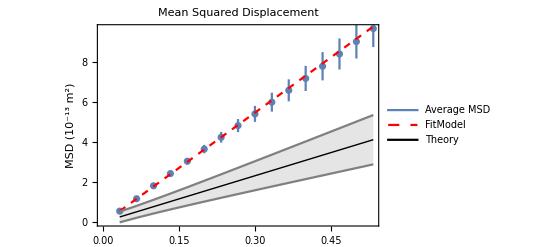

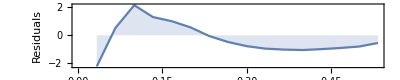

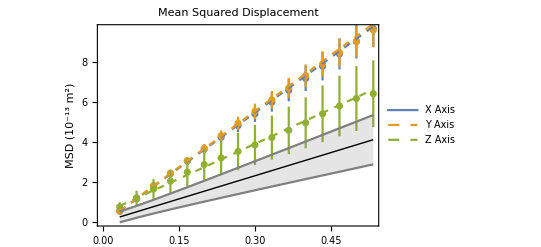

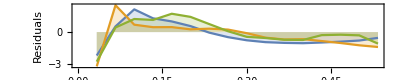

```mathematica
(*Numerical Results*)
Print[]
Print[Style["Numerical Results",Underlined]]
Print["D = ", SetPrecision[ScientificForm@DC,3]," ± ",SetPrecision[ScientificForm@σDC,3]," m^2/s"]
Print["DT = ", SetPrecision[ScientificForm@DCT,3]," ± ",SetPrecision[ScientificForm@σDCT,3]," m^2/s"]
Print["η = ", SetPrecision[ScientificForm@η,3]," ± ",SetPrecision[ScientificForm@ση,3]," Pa s"]
Print["ηT = ", SetPrecision[ScientificForm@ηT,3]," ± ",SetPrecision[ScientificForm@σηT,3]," Pa s"]
Print["R^2 = ", SetPrecision[MSDF["RSquared"],4]]
Print["ν = ", SetPrecision[ν,4]]
Print["χ_ν^2 = ", SetPrecision[χ2ν,4]]
Print["P(χ_ν^2;ν) = ", SetPrecision[P,4]]
Print["d = ", SetPrecision[d,4]]
Print[]
(*Plots*)
MSDσ=MapAt[ErrorBar,Transpose[{MapAt[#/MaxOM&,MSD,{All,2}],σMSD/MaxOM}],{All,2}];
label=StringTemplate["MSD (10^(`OM`) m^2)"][<|"OM"->OM|>];
plot=Show[
ErrorListPlot[MSDσ],
Plot[MSDF[X]/MaxOM,{X,First[Δt],Last[Δt]},
PlotStyle->{Red,Dashed}],
ListLinePlot[{MSDTData,MSDTDataP,MSDTDataM},
PlotStyle->{{Thick,Black},Gray,Gray},
Filling->{2->{3}}],
FrameLabel->{None,label},
PlotLabel->"Mean Squared Displacement",
Frame->True];

MSDPlot=Legended[plot,Placed[LineLegend[{ColorData[97][1],{Dashed,Red},{Thick,Black}},{"Average MSD","FitModel","Theory"},LegendFunction->Panel],{{0.05,0.58},{0,0}}]]
ResPlot=ListLinePlot[Transpose[{Δt,MSDF["StandardizedResiduals"]}],
AspectRatio->1/5,
Frame->True,
Filling->Axis,
FrameLabel->{"Δt (s)","Residuals"}]

(*XYZ Plots*)
MSDσX=MapAt[ErrorBar,Transpose[{MapAt[#/MaxOM&,MSDx,{All,2}],σMSDx/MaxOM}],{All,2}];
MSDσY=MapAt[ErrorBar,Transpose[{MapAt[#/MaxOM&,MSDy,{All,2}],σMSDy/MaxOM}],{All,2}];
MSDσZ=MapAt[ErrorBar,Transpose[{MapAt[#/MaxOM&,MSDz,{All,2}],σMSDz/MaxOM}],{All,2}];
label=StringTemplate["MSD (10^(`OM`) m^2)"][<|"OM"->OM|>];
plotXYZ=Show[
ErrorListPlot[{MSDσX,MSDσY,MSDσZ}],
Plot[{MSDFx[X]/MaxOM,MSDFy[X]/MaxOM,MSDFz[X]/MaxOM},{X,First[Δt],Last[Δt]},PlotStyle->Dashed],
ListLinePlot[{MSDTData,MSDTDataP,MSDTDataM},
PlotStyle->{{Thick,Black},Gray,Gray},
Filling->{2->{3}}],
FrameLabel->{None,label},
PlotLabel->"Mean Squared Displacement",
Frame->True];
MSDPlotXYZ=Legended[plotXYZ,Placed[LineLegend[{ColorData[97][1],{Dashed,ColorData[97][2]},{Dashed,ColorData[97][3]}},{"X Axis","Y Axis","Z Axis"},LegendFunction->Panel],{{0.05,0.58},{0,0}}]]

ResPlotXYZ=ListLinePlot[{
Transpose[{Δt,MSDFx["StandardizedResiduals"]}],
Transpose[{Δt,MSDFy["StandardizedResiduals"]}],
Transpose[{Δt,MSDFz["StandardizedResiduals"]}]},
AspectRatio->1/5,
Frame->True,
Filling->Axis,
FrameLabel->{"Δt (s)","Residuals"}]
```

```mathematica
(*Export Numerical Results & Plot*)
Export["ResultsMSD/MSDPlot.pdf",MSDPlot];
Export["ResultsMSD/Residuals.pdf",ResPlot];
Export["ResultsMSD/MSDPlotXYZ.pdf",MSDPlotXYZ];
Export["ResultsMSD/ResidualsXYZ.pdf",ResPlotXYZ];
Export["ResultsMSD/DC.dat",SetPrecision[DC,3]];
Export["ResultsMSD/errDC.dat",SetPrecision[σDC,3]];
Export["ResultsMSD/DCT.dat",SetPrecision[DCT,3]];
Export["ResultsMSD/errDCT.dat",SetPrecision[σDCT,3]];
Export["ResultsMSD/Eta.dat", SetPrecision[η,3]];
Export["ResultsMSD/errEta.dat",SetPrecision[ση,3]];
Export["ResultsMSD/EtaT.dat",SetPrecision[ηT,3]];
Export["ResultsMSD/errEtaT.dat",SetPrecision[σηT,3]];Export["ResultsMSD/R2.dat",SetPrecision[MSDF["RSquared"],4]];Export["ResultsMSD/DoF.dat",SetPrecision[ν,4]];Export["ResultsMSD/Chi2.dat",SetPrecision[χ2ν,4]];Export["ResultsMSD/P.dat",SetPrecision[P,4]];
Export["ResultsMSD/d.dat",SetPrecision[d,4]];
```